### Facts, so far

It is Sunday, April 4th. The moon is nearly full. The numbers keep growing, and growing fast, so much so that quoting them feels pointless. But still: there are well over a million confirmed cases of the infection worldwide, and more than 300,000 in the US alone. Close to 70,000 people have died, and the daily growth of confirmed cases world-wide has grown by orders of magnitude — from hundreds, to thousands, to tens of thousands.

```mathematica
country[c_]:=Module[{countryMap=<|"Korea, South"->"South Korea"|>,q},q=countryMap[c];If[MissingQ[q],c,q]];
meta[c_]:=Module[{
totalMap=<|"US"->{"1 apr 2020",230000},"Italy"->{"1 apr 2020",125000},"Germany"->{"1 apr 2020",80000},"United Kingdom"->{"1 apr 2020",30000}|>,
growthMap=<|"US"->{"29 mar 2020",20000},"Italy"->{"13 mar 2020",7000},"Germany"->{"2 apr 2020",9000},"United Kingdom"->{"2 apr 2020",1500}|>,
accMap=<||>,
q,m},
m={"country"->CountryData[country[c],"Flag"]};
q=totalMap[c];If[!MissingQ[q],AppendTo[m,"total"->q]];
q=growthMap[c];If[!MissingQ[q],AppendTo[m,"growth"->q]];
q=accMap[c];If[!MissingQ[q],AppendTo[m,"acc"->q]];
m];
label[c_,t_]:=If[MemberQ[c["Properties"],t],Inset[Show[c["country"],ImageSize->30],c[t]],Nothing];
```

```mathematica
world=Import["https://raw.githubusercontent.com/CSSEGISandData/COVID-19/master/csse_covid_19_data/csse_covid_19_time_series/time_series_covid19_confirmed_global.csv"];
worldd=(row↦AssociationThread[Append[world[[1,;;4]],"data"],Append[row[[;;4]],TimeSeries[Transpose[{DateObject[{#,{"Month","/","Day","/","YearShort"}}]&/@world[[1,5;;]],row[[5;;]]}],MetaInformation->meta[row[[2]]]]]])/@Rest[world]//Dataset;
```

```mathematica
cc={"US","Italy","Germany","United Kingdom"};
```

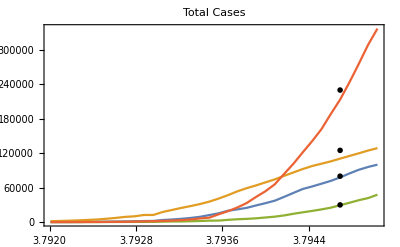

```mathematica
worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],TimeSeriesWindow[#data,{DateObject["1 mar 2020"],Automatic}]&][c↦DateListPlot[c,PlotLegends->((Show[#["country"],ImageSize->40](*//Framed*))&/@c),PlotLabel->"Total Cases",PlotRange->All,
Epilog->(label[#,"total"]&/@c)]]
```

We now know that the screening — at least early screening — was flawed, that the estimates were too low, and that considerably higher number of people got in touch with the virus, either as asymptomatic carriers, or suffering through a bout of mild, inconsequential symptoms, and yet continuing to spread the infection. We will likely never know the full extent of the infection. Still, we have to think about it — these days, it is virtually impossible not to —and rationalize it, understand it, analyze it, and try and behave as rationally and helpfully as we possibly can.

We are in a war. Are we winning? Or losing? Or is all around us just an impenetrable “fog of war,” with no reliable truths that can be used as anchors for rational forward progress? We don’t know. But let’s look at the data as they are, and let’s try to stretch them a bit into the future.

### Case growth: Is there a silver lining?

The total number of cases has been steadily growing in most countries. But the rate of growth has declined in few of the hardest-hit places over the last week or so. Specifically, in Italy, the daily case growth has declined from around 6,000 from the peak in late March to around 4,800 today, a decrease of around 20%. Furthermore, a number of European countries have seen the growth rates stabilize -- in other words, the exponential explosion seems to be giving way to a different, more bearable trend.

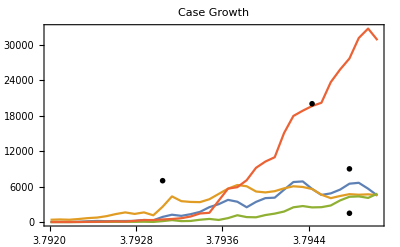

```mathematica
worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],TimeSeriesWindow[Differences[#data,1,2]/2,{DateObject["1 mar 2020"],Automatic}]&][c↦DateListPlot[c,PlotLegends->((Show[#["country"],ImageSize->40](*//Framed*))&/@c),PlotLabel->"Case Growth",PlotRange->All,Epilog->(label[#,"growth"]&/@c)]]
```

A different way to look at the same data is through case acceleration, or the daily change in the rate of growth. What we would want to see is that the (positive) acceleration gives way to deceleration, or negative acceleration, eroding the rate of growth and “flattening the curve.”

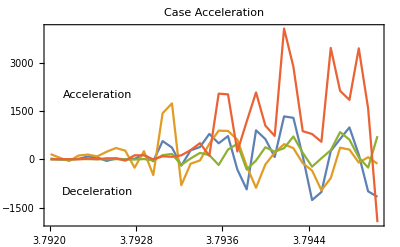

```mathematica
worldd[Select[MemberQ[cc,#["Country/Region"]]∧#["Province/State"]==""&],TimeSeriesWindow[Differences[Differences[#data,1,2],1,1]/2,{DateObject["1 mar 2020"],Automatic}]&][c↦DateListPlot[c,PlotLegends->((Show[#["country"],ImageSize->40](*//Framed*))&/@c),PlotLabel->"Case Acceleration",PlotRange->All,Axes->True,Epilog->{Inset["Deceleration",{"6 mar 2020",-1000}],Inset["Acceleration",{"6 mar 2020",2000}]}]]
```

This is good news indeed, if it is true. According to quantitative epidemiology models, infection growth rate is a bell-shaped curve. Indeed, different forms of these graphs were reported by the US government (see, for example, this article, for a sober assessment of strengths, and weaknesses, of such models). What this means is that, once the growth rate reaches its peak, it starts to decline, eventually (asymptotically...) falling all the way to 0. That is, at least, the theory. Back in the real world, a myriad factors may throw these simple models off track and change their outcomes, including — and that is, indeed, one of the main goals of these modeling exercises — devising different containment policies.

### Hold your nose and model

Once again, a decline in the case growth is great news, and it is really important for it to hold and spread. But in addition to providing some much-needed hope and good news, it also opens doors to studying the dynamics of the epidemic beyond its initial phases when all that is seen is the explosive, exponential growth. So let’s put some heavy-duty machinery to work. The SIR is a work-horse model of the spread of infectious diseases (see, for example, https://en.wikipedia.org/wiki/Compartmental_models_in_epidemiology). “S” in “SIR” stands for “susceptible,” ,”I” for “infected,” and “R” for “recovered.” Initially, the entire population is “susceptible.” As the infection spreads, some of the “susceptible” people become “infected,” reducing the pool of “susceptible” and increasing the pool of “infected.” And as people recover, the similar transfer occurs: “infected” pool shrinks, “recovered” pool grows. Key parameters of the model are constants that define the rate of transfer between “susceptible” and “infected,” and “infected” and “recovered.”

Without going much into technicalities, the SIR model allows for estimating few parameters that “drive” the process, and for extrapolating beyond the present time and peeking into the (not-too-distant) future. To be fair, there is a litany of possible issues affecting these estimates. But before listing them, let’s look at the results and try to interpret them at the face value.

```mathematica
ff[Ix_,α_?NumericQ,β_,γ_,J1_,J2_,NN_,n1_,n2_]:=Module[{nn,sol,J,z},
nn=Ix//Length;
sol=NDSolve[{D[J[t],{t,2}]==D[J[t],t](β/NN Exp[α-(β/NN)J[t]]-γ),J[n1]==J1,J[n2]==J2},J,{t,1,nn}][[1]];
z=Table[Evaluate[J[t]/.sol],{t,nn}]-Ix;
z.z]
```

```mathematica
est1[c_,start_:Automatic,ρ_:1]:=Module[{NN,Is,Id,Iv,nn,Ix,sol,sol1,Iz,n1=10,n2=20,ϵ=.99,β=57,γ=.0001,nex=8},
NN=(CountryData[country[c],"Population"]// Normal)ρ;
Is0=Is=worldd[Select[#["Country/Region"]==c∧#["Province/State"]==""&],TimeSeriesWindow[#data,{start,Automatic},IncludeWindowTimes->True]&][[1]];
Iv=Is["Values"];
Id=Is["Dates"];
nn=Is["PathLength"];
Ix=Accumulate[Iv];
sol=NMinimize[{ff[Ix,α,β,γ,J1,J2,NN,n1,n2],(1-ϵ)Ix[[n1]]≤J1≤(1+ϵ)Ix[[n1]],(1-ϵ)Ix[[n2]]≤J2≤(1+ϵ)Ix[[n2]]},{α,J1,J2}]//Echo;
sol1=NDSolve[{D[JJJ[t],{t,2}]==D[JJJ[t],t](β/NN Exp[α-(β/NN)JJJ[t]]-γ),JJJ[n1]==J1,JJJ[n2]==J2}/.sol[[2]],JJJ,{t,0,nn}][[1]];
Iz0=Iz=TimeSeries[Table[Evaluate[JJJ[t]/.sol1],{t,0,nn+nex}]//Differences, {Is["FirstDate"],Automatic,"Day"}];
DateListPlot[{Is,Iz},PlotRange->All,
PlotLegends->{"Actual","Estimate"},
PlotLabel->(Show[CountryData[country[c],"Flag"],ImageSize->40](*//Framed*))]
]
```

First, Italy. The case growth has been slowing over the last week or so, and the model recognizes this slow-down. Extrapolating over the next two weeks suggests — quite optimistically — that the growth-of-growth, or case acceleration, may have already peaked.

{2.22763×10^9,{α→11.952,J1→53891.,J2→328935.}}

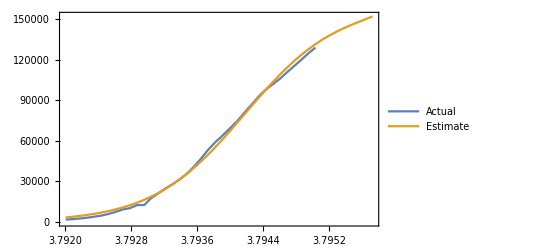

```mathematica
est1["Italy","1 mar 2020"]
```

Elsewhere in Europe, the results are mixed -- from Germany, where the case growth seems to be showing signs of arresting in two weeks, to United Kingdom, where the signs of slowing are much more muted.

{1.85351×10^8,{α→12.2309,J1→838.953,J2→21418.2}}

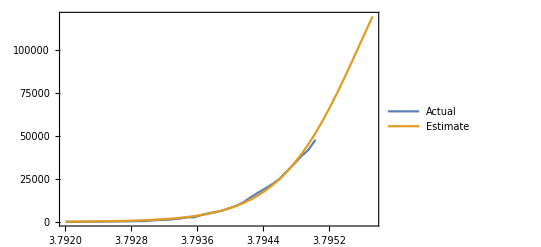

```mathematica
est1["United Kingdom","1 mar 2020"]
```

{4.78312×10^9,{α→12.3209,J1→4859.26,J2→102287.}}

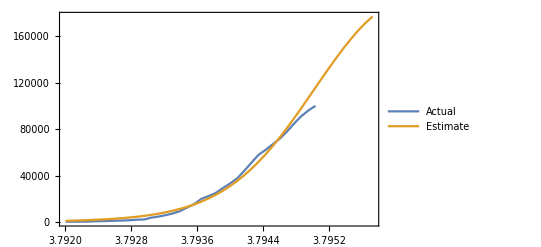

```mathematica
est1["Germany","1 mar 2020"]
```

And in the US, the model suggests two very difficult weeks, followed by some respite and subsequent slowing. In that period, the total number of cases is estimated to climb over 800,000. But this is estimated to be the peak of growth rate, and the US may see some slowing in the case growth towards the end of April.

{2.60483×10^10,{α→13.9521,J1→78.8359,J2→108625.}}

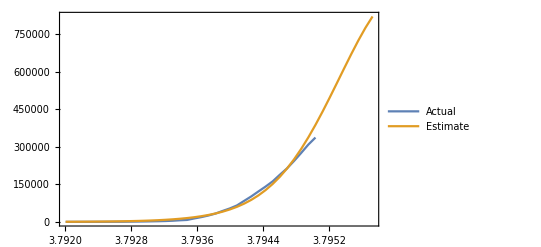

```mathematica
est1["US","1 mar 2020"]
```

Let’s be honest, though. These models are not a crystal ball. Nothing is. They come with the whole slew of more-or-less indefensible assumptions. But the proof is, as always, in the pudding: for as long as they resemble the reality in-sample, and for as long as we don’t push them too far, they may provide a reasonable baseline to think about proximate future, based on what we know today. And that is the point. Two, actually, as far as the US is concerned:

    Total number of cases is likely to grow to close to 1,000,000 by the end of the month...
    ... but, by then, we should see the spread slowing and daily case growth declining

### Symmetry of the S-shaped curve

What will come next? The model itself can’t be pushed that far outside of the time interval used to calibrate it. But we can simply postulate that the rate of decline will, at least to some extent, mimic the spread, and make for a symmetric S-shaped curve: that, once the case growth rate reaches its peak, the time will flow as if in reverse. Let’s take a look at what would that mean for the US. But first, let’s take a look at the projected growth of daily cases in the US.

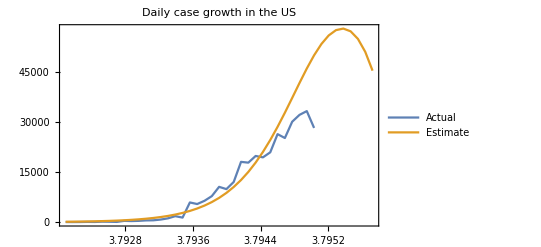

```mathematica
{Is0//Differences,Iz0//Differences}//DateListPlot[#,PlotLegends->{"Actual","Estimate"},PlotLabel->"Daily case growth in the US"]&
```

```mathematica
Iz1=TimeSeriesWindow[TimeSeries[Prepend[Iz0["Values"]//Differences//Reverse//Accumulate,0]+Iz0["LastValue"],{Iz0["LastDate"],Automatic, "Day"}],{Automatic, "2 May 2020"}]
```

TimeSeries[…]

This picture sends two messages. First, the model estimates that the growth will peak somewhere around 50,000 cases per day around mid-April. And second, it seems to be out-running actual observations for last several days. This may be a mirage, or it may be real, and the growth rate in the US may already be slowing relative to the pace from the last month. Social distancing at work? Let’s hope so.

Be it as it may, the growth forecast allows us to complete the S-shaped curve of case growth, by inverting the trajectory so far around the point of maximal growth.

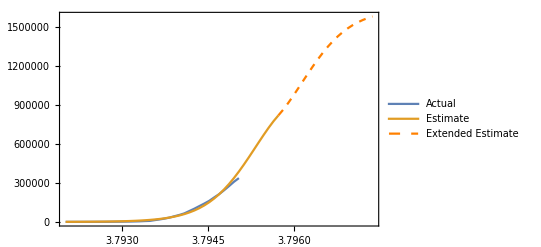

```mathematica
{Is0,Iz0,Iz1}//DateListPlot[#,PlotLegends->{"Actual","Estimate","Extended Estimate"},PlotStyle->{Automatic,Automatic,{Orange,Dashed}},PlotLabel->(Show[CountryData["US","Flag"],ImageSize->40])]&
```

According to this picture, the US will stabilize some time in May, with the total case load eventually reaching 1.5 million. Then, perhaps a month later, and three months from now, we may look towards the Independence Day with some hope.

### Markets, a mirror of our collective psyche

Financial markets matter. In times of a global pandemic, they matter less. Indeed, talking about “stocks that are going to pop” as thousands are dying can easily be seen as vulgar. But markets offer something else: a thermometer of our collective psyche. In good times, markets are driven by the cacophony of financial data, some of it consistent, some of it conflicting, but most relevant. In bad times, however, the market’s focus shrinks to a single issue. The dot-com bubble bursting. Banks falling. Or, presently, the pandemic spreading.

The exhibit below shows the S&P 500 level from its peak at the end of February (yes, indeed, that is only few short weeks ago), correlated with the case growth in the US (technically, in a log-log space). It suggests that the overall damage done by the pandemic ebbs and flows with the growth of the case load. Markets — and, assuming that financial markets do indeed reflect the collective psyche, the way we feel towards the pandemic — are looking forward to the point when the tide turns, and when the positive growth gives way to the negative growth. Acceleration matters, in this case as a milepost of the tide turning.

Another interesting aspect of the graph below is the relatively tight “channel” that the case growth / S&P 500 levels (technically, since the graph is in the log space, that should really read “returns” and not “levels”) fall  in. While the pandemic remains top of mind, it provides a recipe of how the market “prices” (yes, that does sound vulgar...) the pandemic. The top 50,000/day case growth is consistent with the S&P between 2300 and 2400. And once it breaks the pattern, it will hopefully mean that the worst is over and that Mr. Market is, slowly, returning to its previously-scheduled program, together with the MLB and NFL and the new school year...

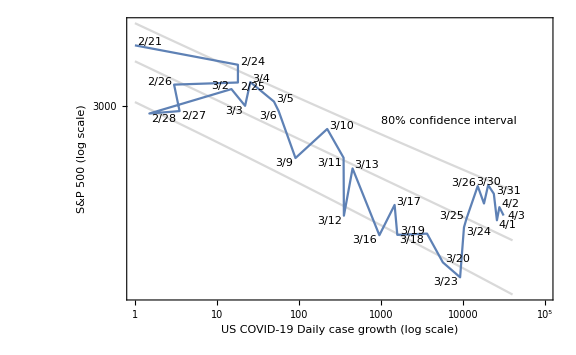

```mathematica
sp = Module[{USg,spy,dates,USg1,spy1,data,g1,e,ci,g2},
USg = worldd[Select[#["Country/Region"]=="US"∧#["Province/State"]==""&],TimeSeriesWindow[Differences[#data,1,2]/2,{DateObject["20 feb 2020"],Automatic}]&][[1]];
spy=FinancialData["SPY","Jan. 1, 2020"]//TimeSeries;
dates = Intersection[USg["Dates"],spy["Dates"]];
USg1 = TimeSeriesResample[USg,{dates}];
spy1=TimeSeriesResample[spy, {dates}];
data=Transpose[{spy1["Dates"],10spy1["Values"](* / spy1["FirstValue"]*),USg1 ["Values"]}];
g1=ListLogLogPlot[Labeled[{#[[3]],#[[2]]},DateString[#[[1]],{"MonthShort","/","DayShort"}]]&/@data,Joined->True];
e=NonlinearModelFit[Select[{#[[3]],#[[2]]}&/@data,#[[1]]>0∧#[[2]]>0&],Exp[α+β Log[xx]],{α,β},xx];
ci=e["SinglePredictionBands",ConfidenceLevel->.8];
g2=LogLogPlot[{e["Function"][xx],ci[[1]],Labeled[ci[[2]],"80% confidence interval",1000]},{xx,1,40000},PlotStyle->LightGray];
Show[g2,g1,PlotRange->{{0,11.5},All},FrameLabel->{"US COVID-19 Daily case growth (log scale)","S&P 500 (log scale)"},Frame->{{True,False},{True,False}},ImageSize->Large]
]
```

And in closing, please allow me a personal note. I’ve been around the financial markets for a quarter of a century, and around this earth for more than twice that much. That on its own is not all that much, but it does canvas few interesting time periods: something we used to call “the Asian crisis” — and no, it had nothing to do with strands of protein that will our own cells into misbehaving —then the dot-com bubble bursting, then the 9/11, and finally the financial crisis. And while the present times always feel different — simply because they are “now” — it is not just the arrogance of the present to claim that, this time around, it really, truly is different. No model, or estimate, or forecast may tell us anything useful right now. But this much is certain: today’s present will, eventually, turn into some other day’s past. It always does.